```mathematica
k = 12;
h = 0.16;

df[x_] := -k*x
f[0.0] = 1;
f[t_] := f[t-h] + df[f[t-h]]*h

g[0.0] = 1;
g[t_] := g[t-h] / (1 + h*k)

Slider[Dynamic[k], {0, 50}]
Slider[Dynamic[h], {0.05, 1}]

Dynamic[Show[Plot[E^(-k*t), {t, 0, 1}, PlotRange->{-1, 1}], DiscretePlot[{f[t], g[t]}, {t, 0, 1, h}, Joined->True, PlotRange->{-1, 1}]]]
```

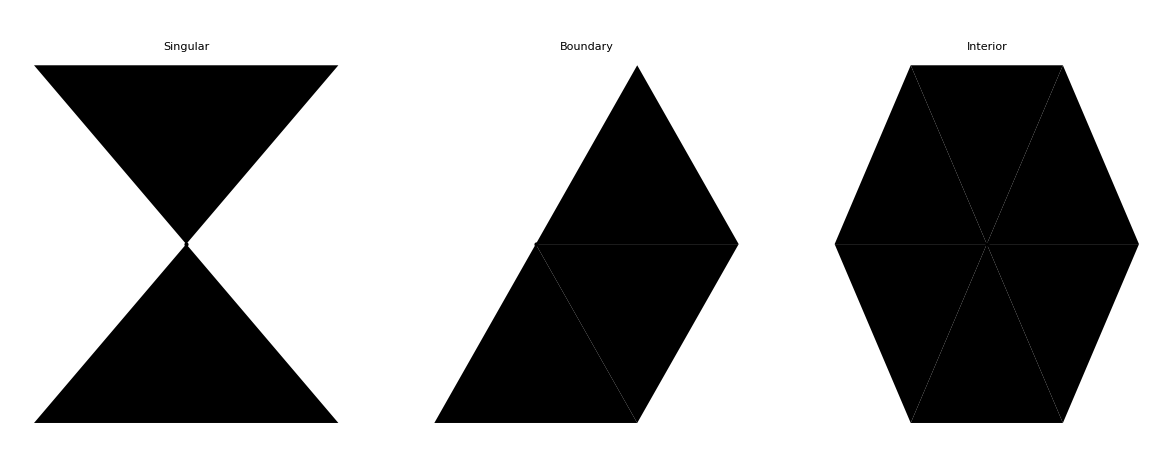

/Users/miles/Kiln/projects/fem/Figures.pdf

```mathematica
apex = {1/2, Sqrt[3]/2};
tri = {{0,0}, {1,0}, apex};
style = {FaceForm[None],EdgeForm[Blue],AbsolutePointSize[8]};

fig = GraphicsRow[{
Graphics[{Polygon[tri], Rotate[Polygon[tri], 180Degree, apex],Point[apex]},PlotLabel->"Singular", BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex], Point[apex]},PlotLabel->"Boundary",BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex],
Rotate[Polygon[tri],180Degree, apex],
Rotate[Polygon[tri],240Degree, apex],
Rotate[Polygon[tri],300Degree, apex] ,Point[apex]},PlotLabel->"Interior", BaseStyle->style]}]

Export[FileNameJoin[{NotebookDirectory[], "figures.pdf"}],fig]
```

{{0.,20.},{-20.,-20.},{-15.2695,-4.58152}}

{{0.72,0.16},{0.72,0.08},{1.2,0.16}}

{{0.48,0.08},{0.4,0.08},{0.96,0.12}}

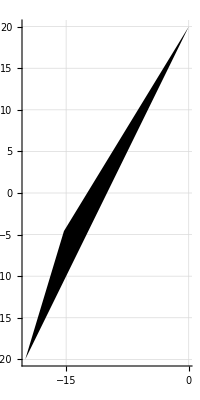

```mathematica
tri1 = {{0.000000,20.000000},{-20.000000,-20.000000},{-15.269472,-4.581519}}
tri2 = {{0.720000,0.160000},{0.720000,0.080000},{1.200000,0.160000}}
tri3 = {{0.480000,0.080000}, {0.400000,0.080000}, {0.960000,0.120000}}
Graphics[{Polygon[tri1]},Axes->True, GridLines->True]
```

```mathematica
tris={{{0.000000,0.000000},{4.000000,0.000000},{0.624243,0.085180}},{{4.000000,0.000000},{0.000000,4.000000},{0.718002,0.592209}},{{0.624243,0.624243},{0.624243,0.085180},{0.718002,0.592209}},{{0.624243,0.085180},{4.000000,0.000000},{0.718002,0.592209}},{{0.000000,4.000000},{0.000000,0.000000},{0.108618,0.624243}},{{0.000000,0.000000},{0.624243,0.085180},{0.108618,0.624243}},{{0.624243,0.624243},{0.000000,4.000000},{0.342927,0.667571}},{{0.000000,4.000000},{0.108618,0.624243},{0.342927,0.667571}},{{0.624243,0.085180},{0.624243,0.624243},{0.342927,0.667571}},{{0.108618,0.624243},{0.624243,0.085180},{0.342927,0.667571}},{{0.000000,4.000000},{0.624243,0.624243},{0.718002,0.592209}}}
pr={0.483627,0.592209}
edges={{{0.624243,0.085180},{0.718002,0.592209}},{{0.718002,0.592209},{0.624243,0.624243}},{{0.000000,0.000000},{0.624243,0.085180}},{{0.624243,0.085180},{0.108618,0.624243}},{{0.108618,0.624243},{0.000000,0.000000}},{{0.624243,0.624243},{0.342927,0.667571}},{{0.108618,0.624243},{0.624243,0.085180}},{{0.342927,0.667571},{0.108618,0.624243}}}



Graphics[{FaceForm[Black],EdgeForm[Blue], Polygon/@tris, Pink, Point[pr]}]
Graphics[{FaceForm[None],EdgeForm[Blue], Line/@edges, Pink, Point[pr]}]
```

{{{0.,0.},{4.,0.},{0.624243,0.08518}},{{4.,0.},{0.,4.},{0.718002,0.592209}},{{0.624243,0.624243},{0.624243,0.08518},{0.718002,0.592209}},{{0.624243,0.08518},{4.,0.},{0.718002,0.592209}},{{0.,4.},{0.,0.},{0.108618,0.624243}},{{0.,0.},{0.624243,0.08518},{0.108618,0.624243}},{{0.624243,0.624243},{0.,4.},{0.342927,0.667571}},{{0.,4.},{0.108618,0.624243},{0.342927,0.667571}},{{0.624243,0.08518},{0.624243,0.624243},{0.342927,0.667571}},{{0.108618,0.624243},{0.624243,0.08518},{0.342927,0.667571}},{{0.,4.},{0.624243,0.624243},{0.718002,0.592209}},Null}

{0.483627,0.592209}

{{{0.624243,0.08518},{0.718002,0.592209}},{{0.718002,0.592209},{0.624243,0.624243}},{{0.,0.},{0.624243,0.08518}},{{0.624243,0.08518},{0.108618,0.624243}},{{0.108618,0.624243},{0.,0.}},{{0.624243,0.624243},{0.342927,0.667571}},{{0.108618,0.624243},{0.624243,0.08518}},{{0.342927,0.667571},{0.108618,0.624243}},Null}

-Graphics-

-Graphics-

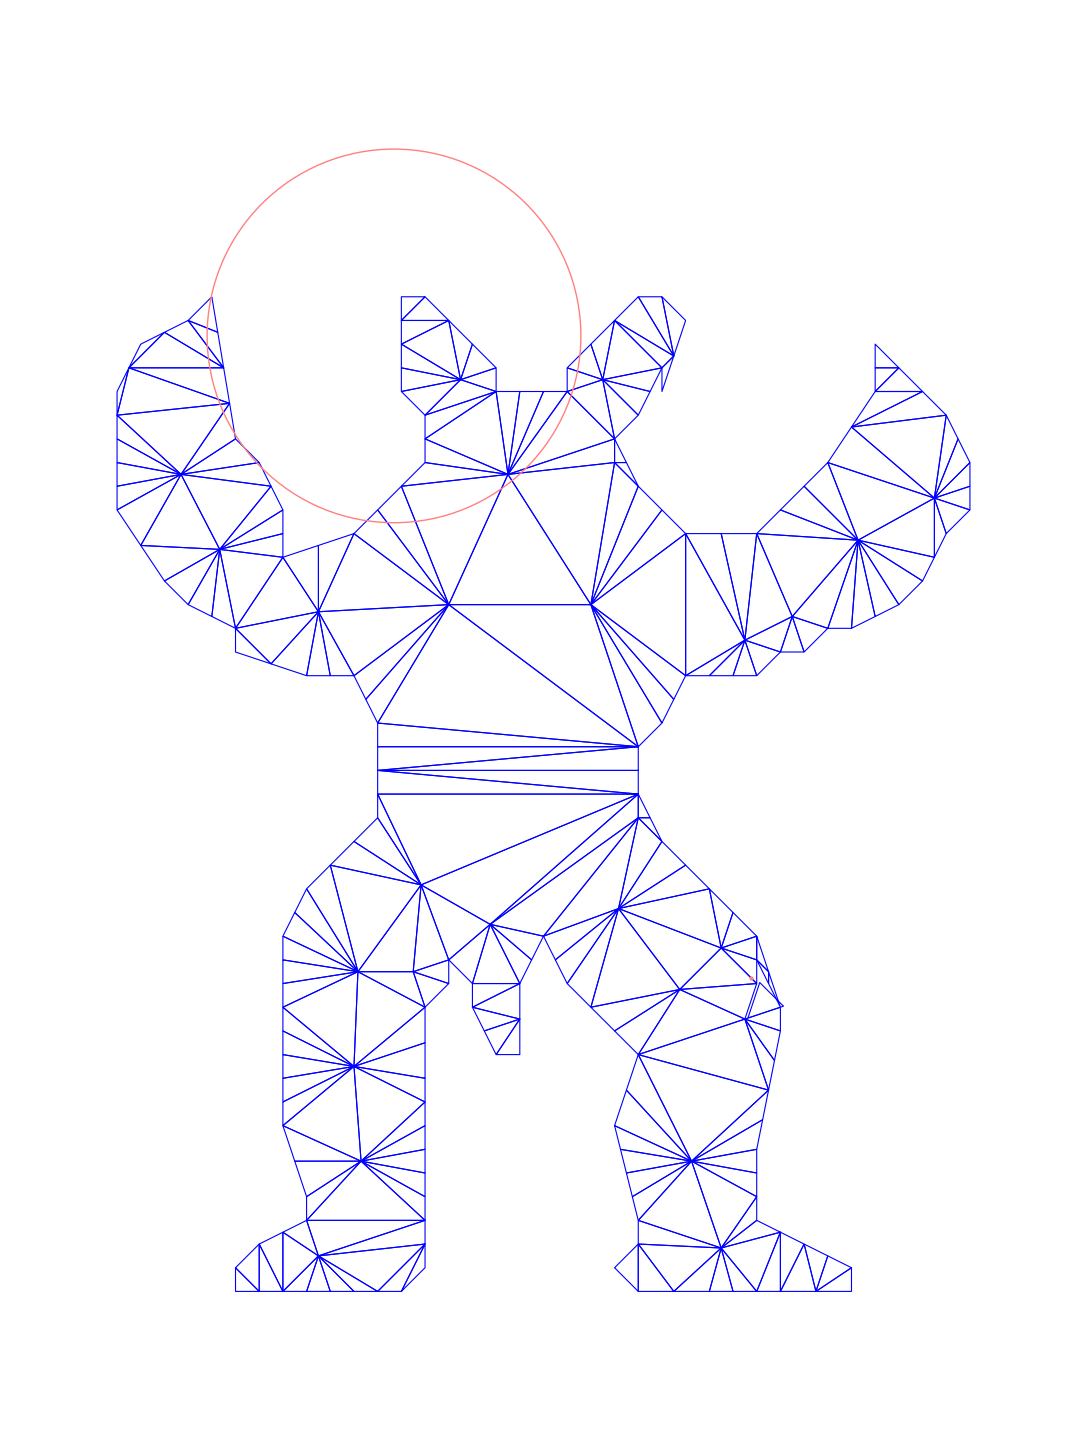

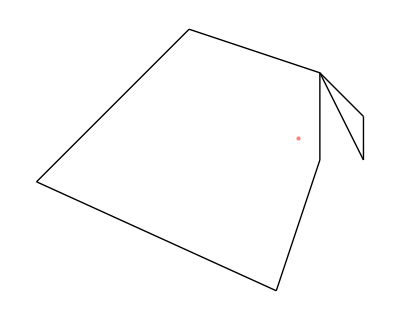

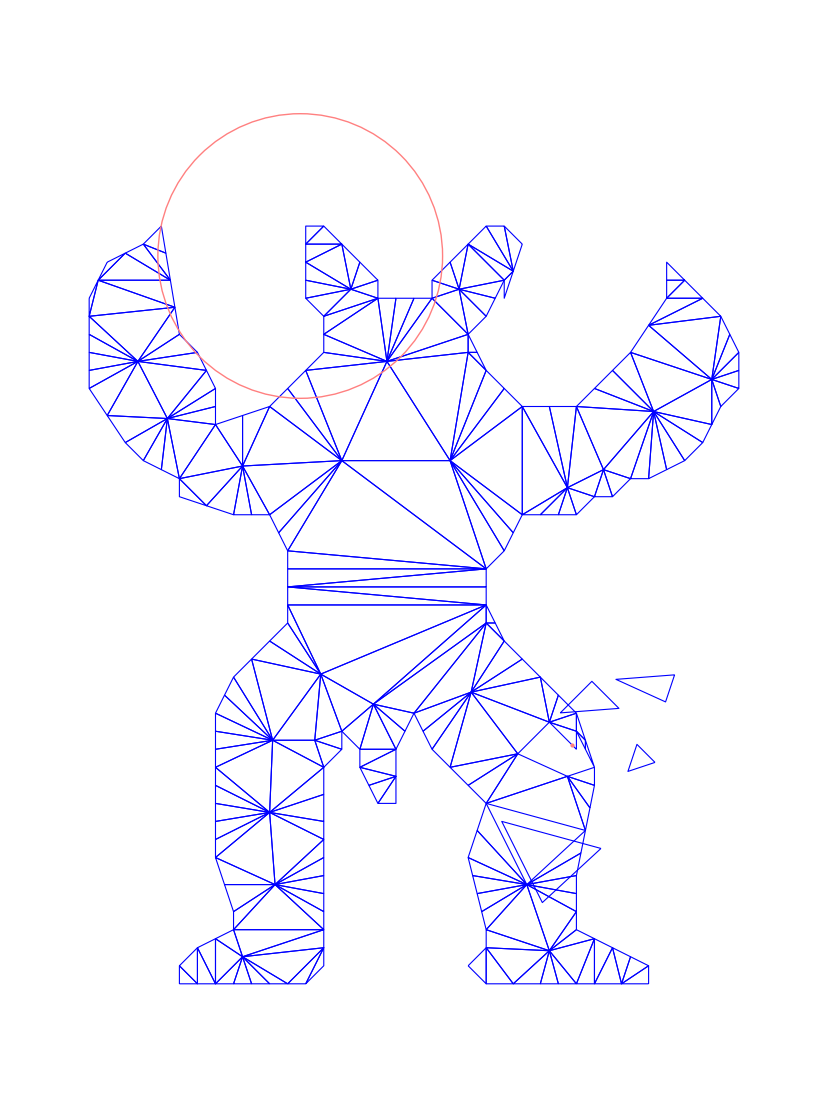

-Graphics-

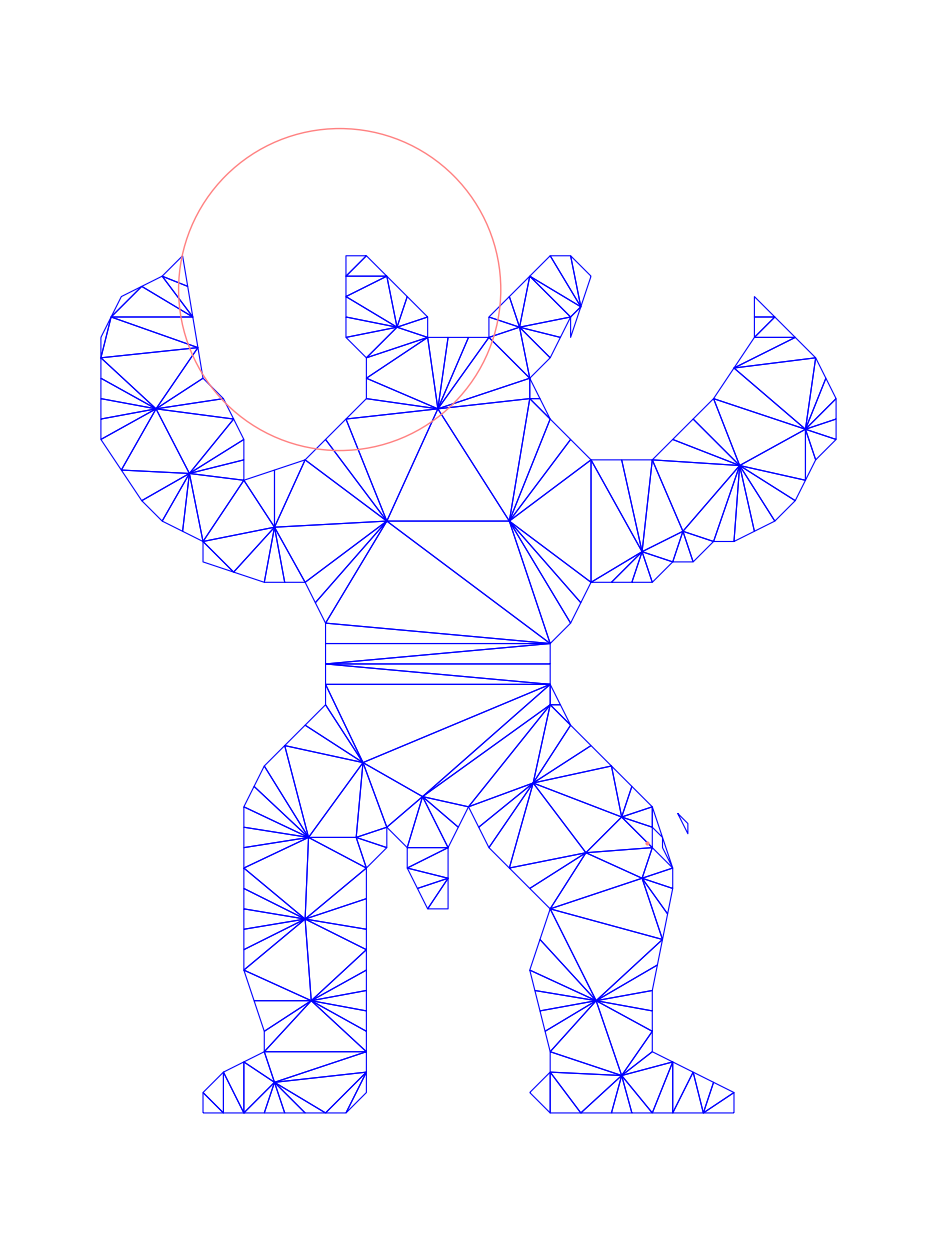

-Graphics-

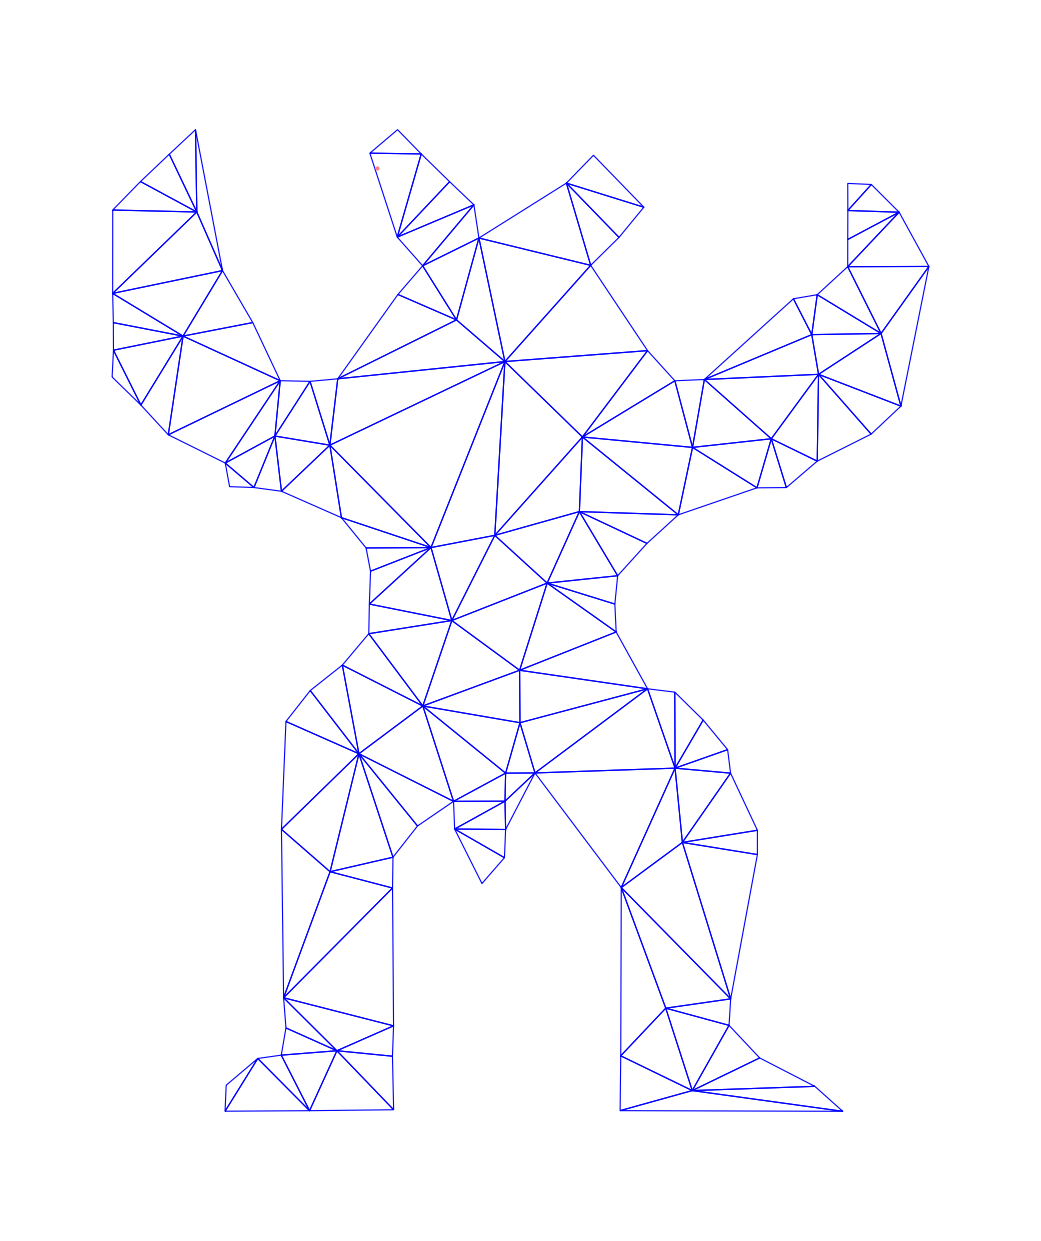

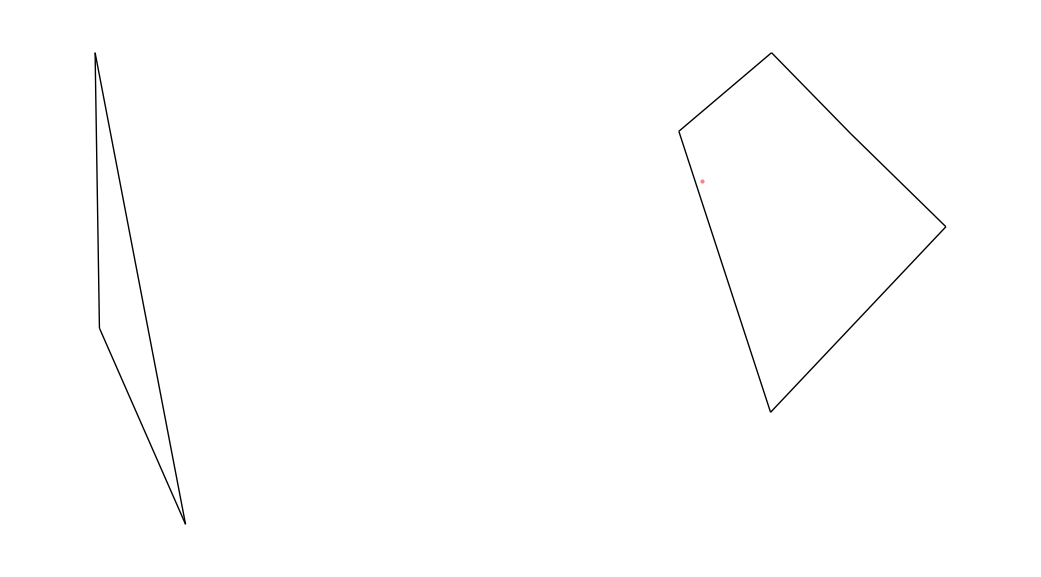

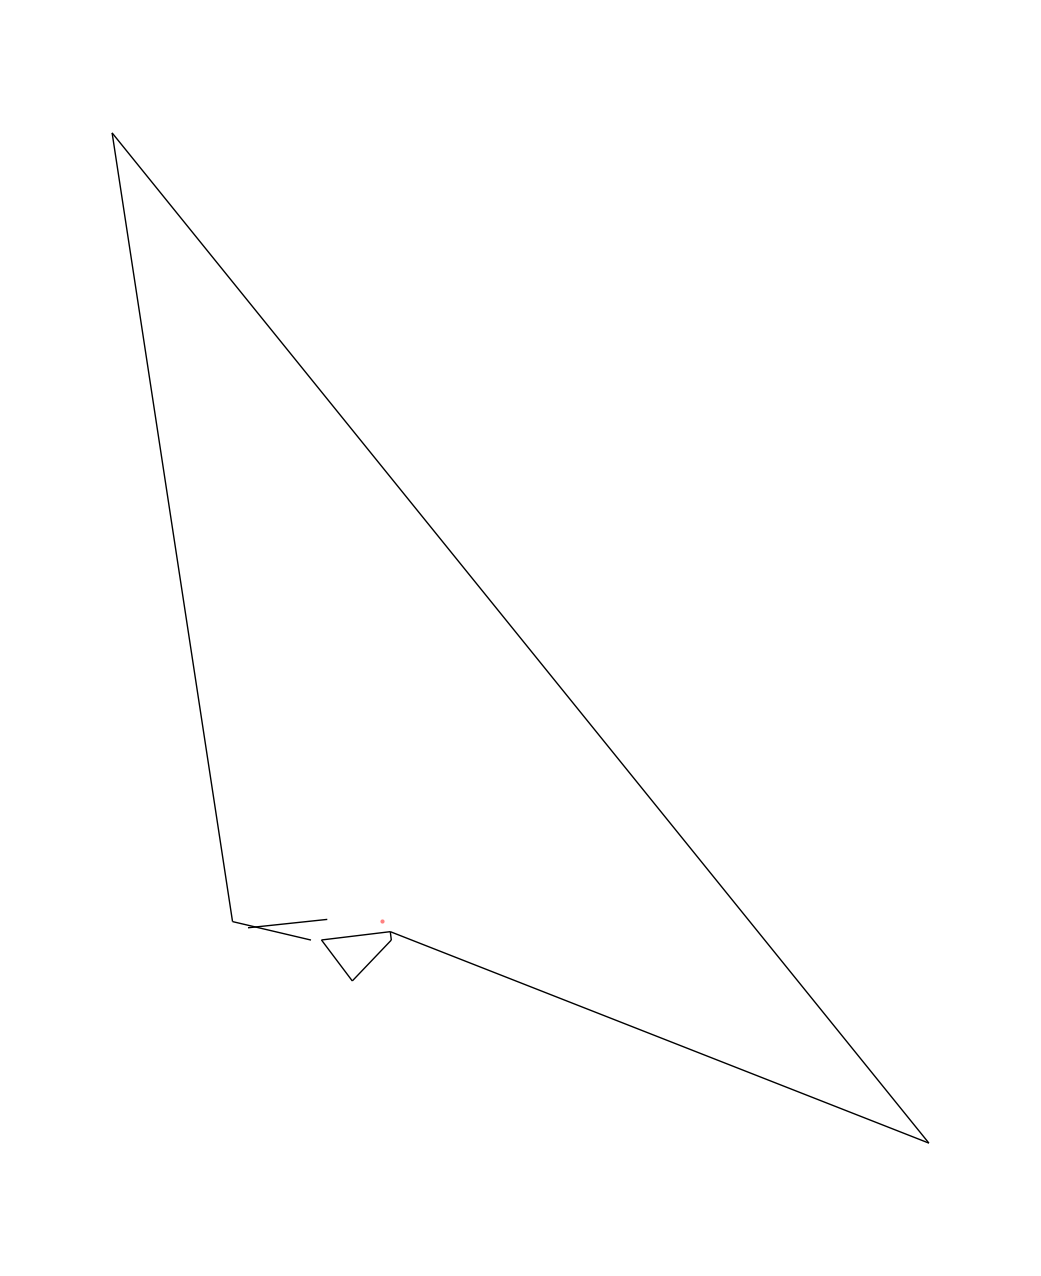

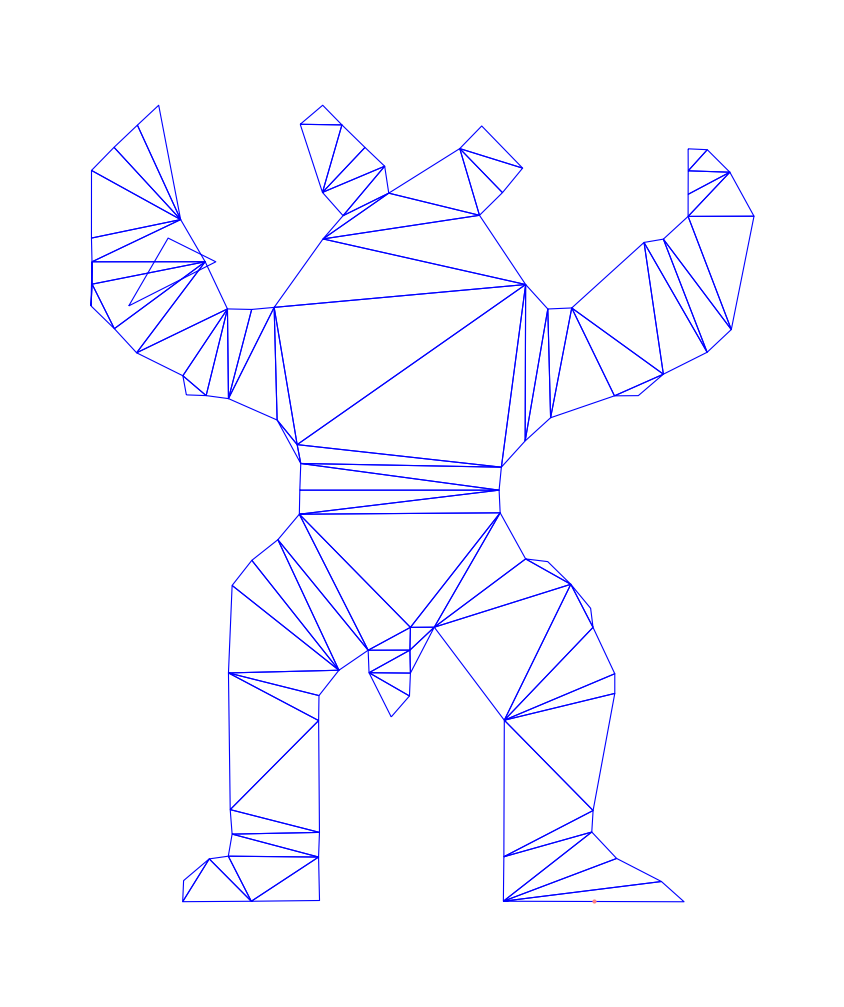

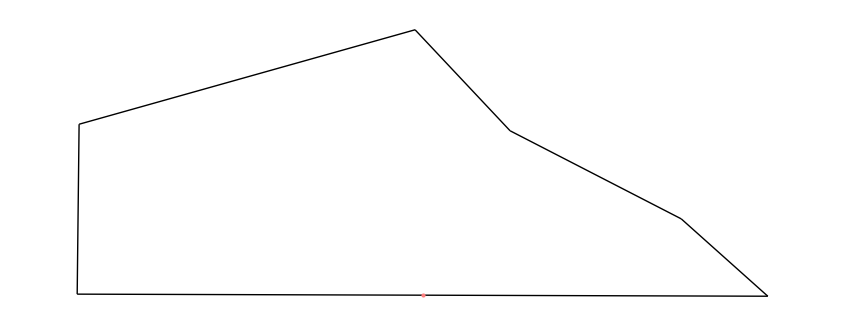

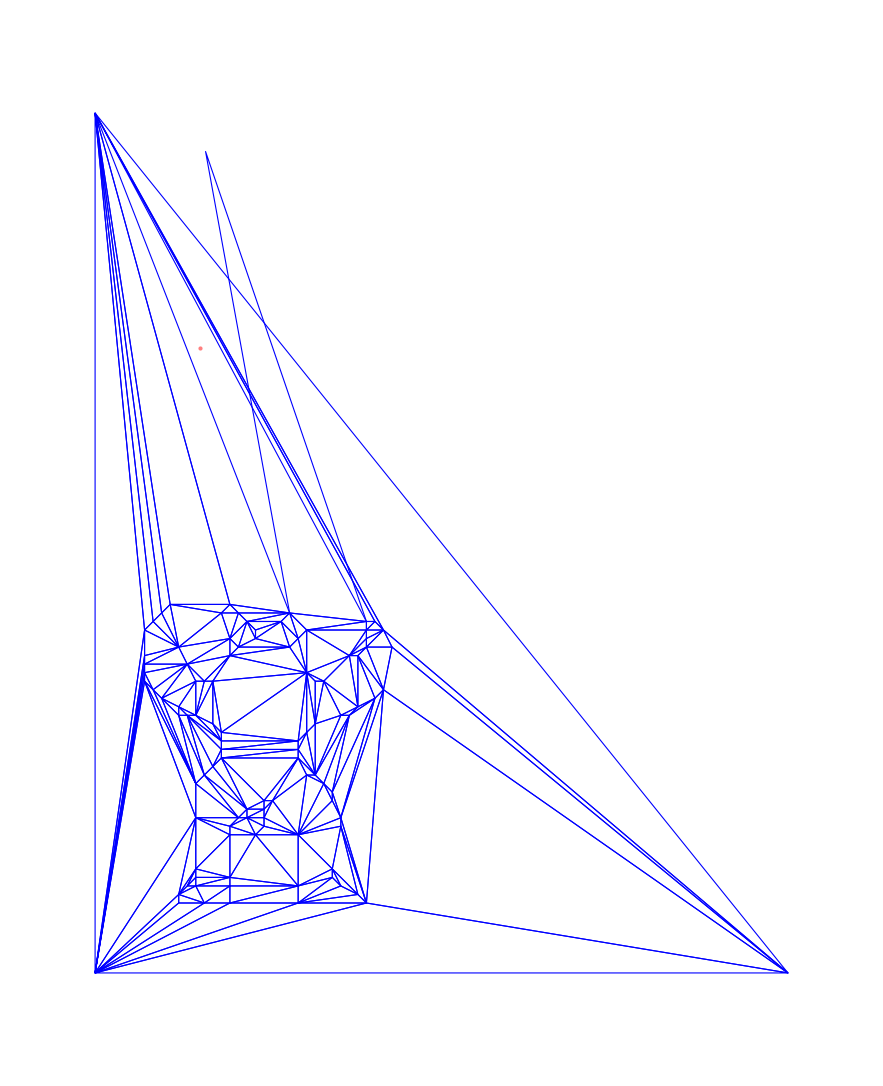

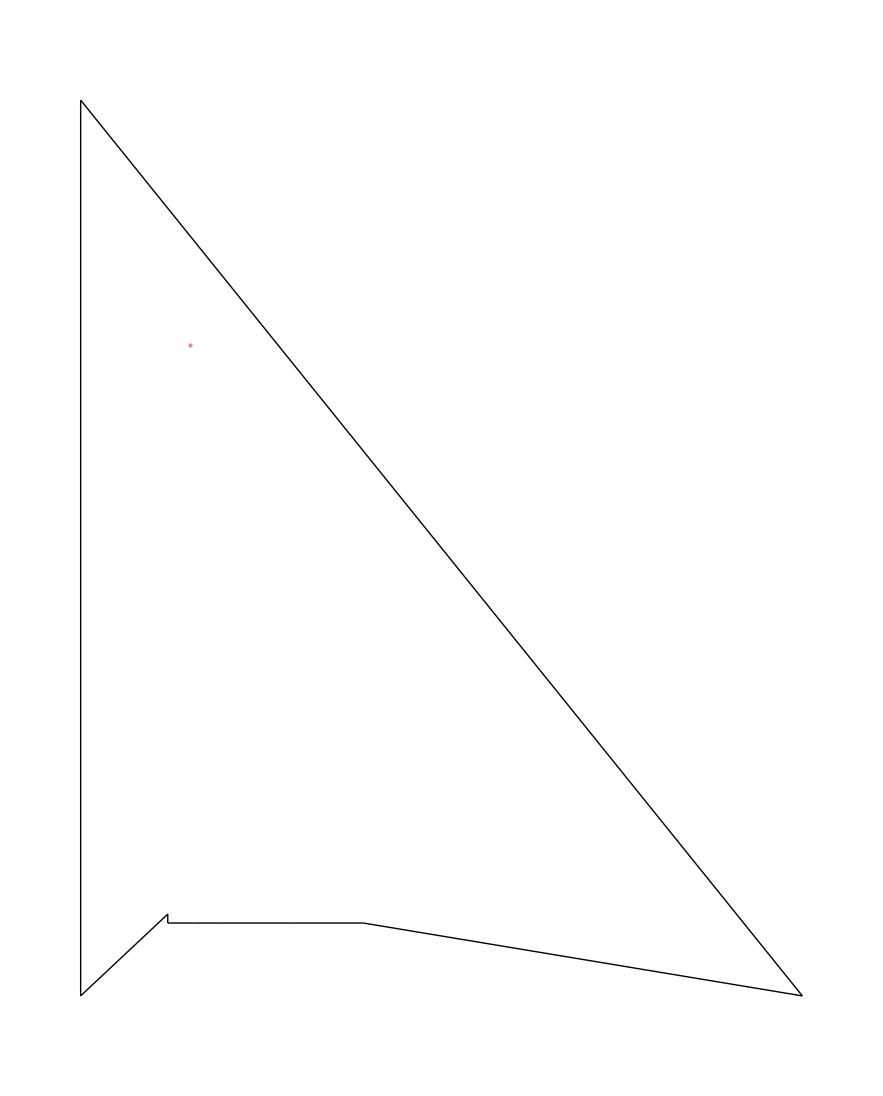

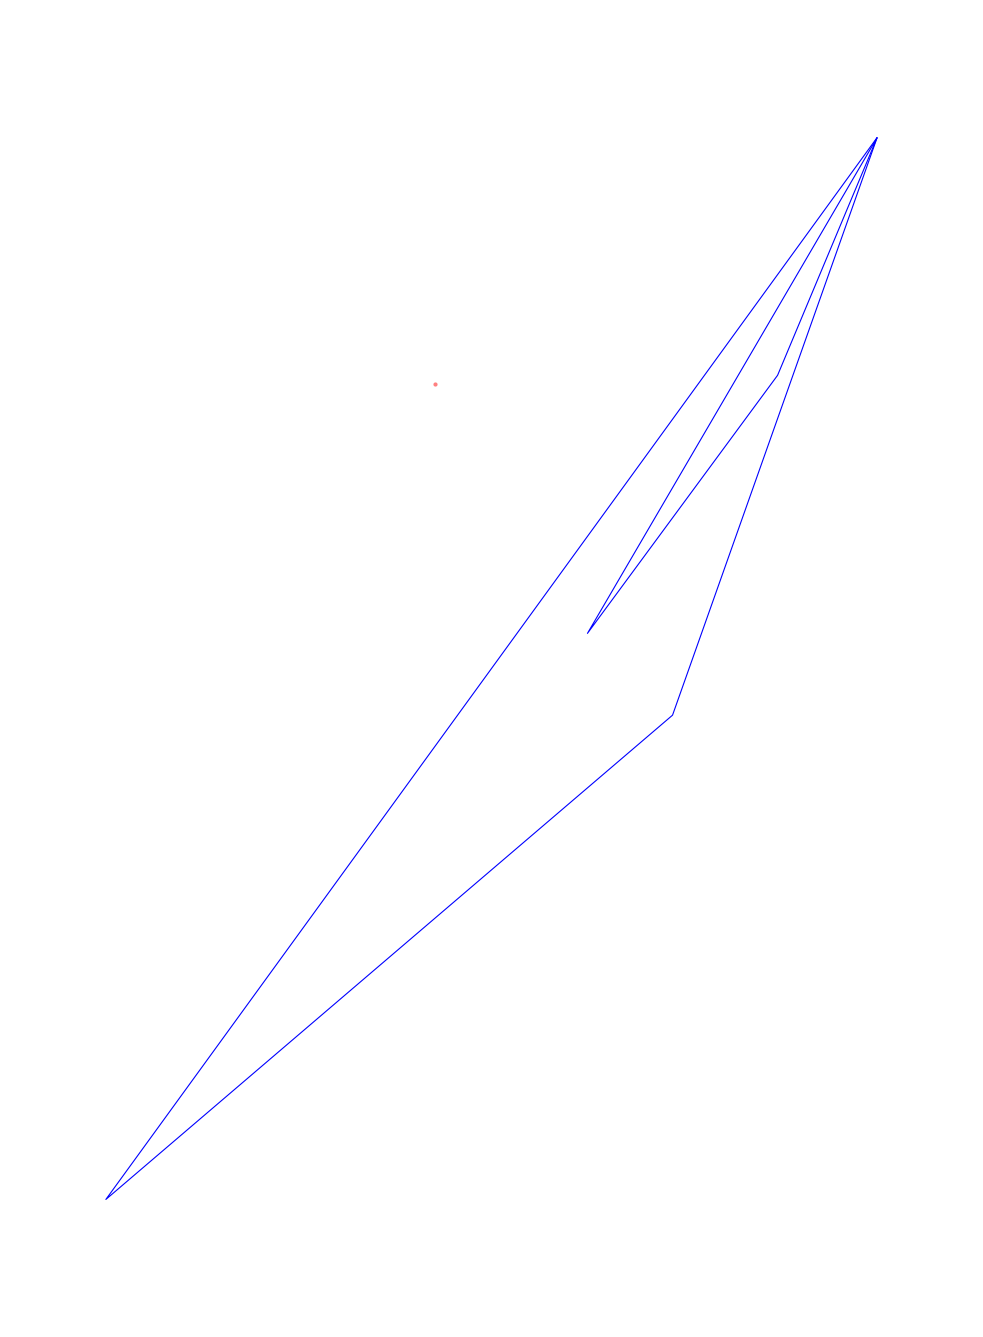

1

0.1

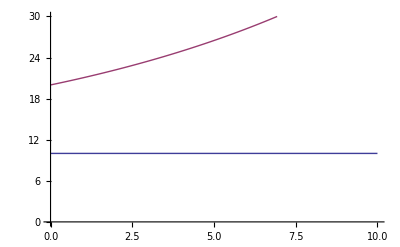

```mathematica
a = 1
k = 0.1

Plot[{a/k, (E^(k(t) ) + a) /k}, {t, 0, 10}, PlotRange->{0,30}]
```

{{0.111703,1.17912},{0.33559,1.49799},{-0.078785,1.49077}}

{0.129972,1.40433}

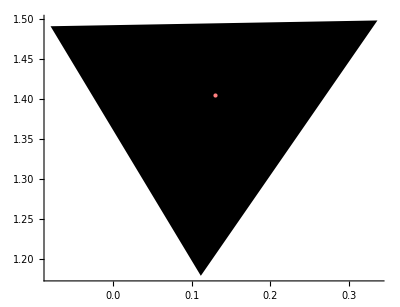

```mathematica
atri = {{0.111703,1.179124},{0.335590,1.497993},{-0.078785,1.490770}}
apt = {0.129972,1.404330}
Graphics[{Polygon[atri],Pink, Point[apt]}, Axes->True]
```